ABM Investments model 
Run and display of results
     
HAPPI (Heterogenous Agent-based Power Plant Investments)
2021, June 22

© Kristian Lindgren, kristian.lindgren@chalmers.se

This implementation has been used for the paper by 
Jinxi Yang, Christian Azar and Kristian Lindgren:
“Financing the transition towards carbon neutrality - an agent-based approach to modelling investment decisions in the electricity system”
(submitted for publication 2021)

This notebook contains command for running the model, “modelRun”, 
and then follows a large number of graphics output commands.

```mathematica
(* for controlling randomness if one wants to repeat same runs... *)
(* this can be skipped *)
```

```mathematica
SeedRandom[863354877];
```

```mathematica
(* running the code *)
```

```mathematica
endTime=80; xTime=40;
modelRun[endTime+xTime];
```

```mathematica
Dynamic["time: "<>ToString[runTime]]
```

```mathematica
Installed capacity
```

```mathematica
figDynCapac=Dynamic[If[runTime>6,graphDynCapitalL[tout+1]]]
```

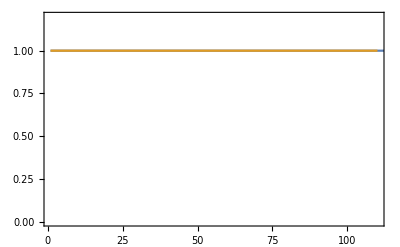

```mathematica
ListLinePlot[{demFactor,Table[1,{endTime+xTime}]},PlotRange->{{1,endTime+xTime},{0,1.2Max[demFactor[[1;;endTime]]]}},AxesOrigin->{1,0},Frame->True]
```

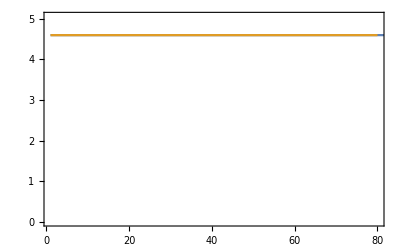

```mathematica
ListLinePlot[{priceGas,Table[runCostGas0,{endTime}]},PlotRange->{{1,endTime},{0,1.1Max[priceGas[[1;;endTime]]]}},AxesOrigin->{1,0},Frame->True]
```

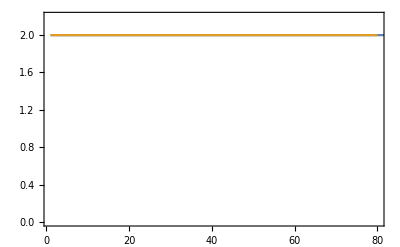

```mathematica
ListLinePlot[{priceCoal,Table[runCostCoal0,{endTime}]},PlotRange->{{1,endTime},{0,1.1Max[priceCoal[[1;;endTime]]]}},AxesOrigin->{1,0},Frame->True]
```

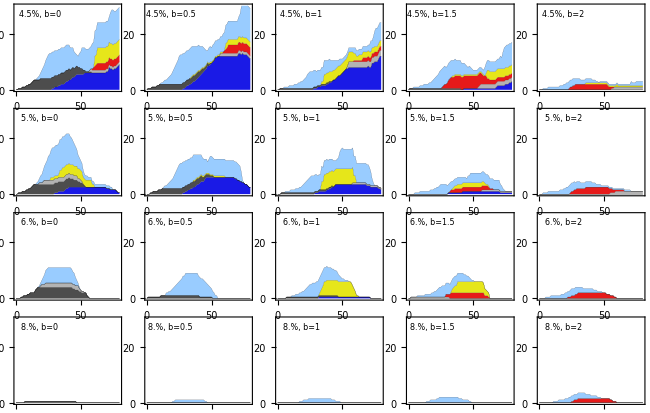

```mathematica
plotTime=endTime;
capTable=Table[graphDynCapitalCompLSNewBkrL[plotTime,i,30],{i,1,numComp}];
capGrid=Partition[capTable,5];
gridCapacity=GraphicsGrid[capGrid,Spacings->{Scaled[0.04],Scaled[0.04]},ImageSize->650]
```

```mathematica
Export["capacityComp90.pdf",gridCapacity];
```

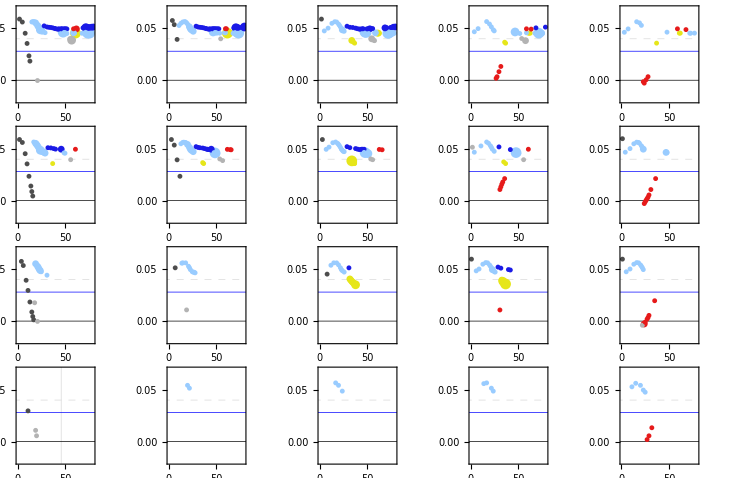

```mathematica
plotTime=90;
plotTime=endTime;
markers=Flatten[Table[Table[{"●",2size+3},{6}],{size,{4,3,2,1}}],1];
maxSize=4;
colorsT=colors[[1;;6]];
Table[irrCalcTable[plant,t]=irrCalc[plant,t],{plant,plantTypeList},{t,1,plotTime}];
irrTable=Table[
ListPlot[
Table[
Flatten[Join[Table[
Table[If[irrCalcTable[plant,t]≠0&&(investComp[plant,t,company]==size ||(size==maxSize&& investComp[plant,t,company]>size)),irrCalcTable[plant,t],-10],{plant,plantTypeList}]
,{size,{4,3,2,1}}]]]
,{t,1,plotTime}]ᵀ
,PlotRange->{-0.02,0.07},PlotStyle->colorsT,ImageSize->260,AspectRatio->0.8,FrameStyle->Directive[8],
GridLines->{If[companyState[[company]]≠"alive",{companyState[[company]]},{}],{{0.04(1-fracInvest),Blue},{0.04,Dashed},{0,Black}}},
GridLinesStyle->{Directive[Thickness[0.008],Red],Thickness[0.005]},
PlotMarkers->markers,
Frame->True,
Epilog->Inset[Style[
ToString[companyCharacteristics[[company,1]]*100]<>"%, "<>
"b="<>ToString[companyCharacteristics[[company,2]]]
,Directive[8]],{160,-0.03}]],
{company,1,numComp}];
irrGrid=Partition[irrTable,5];
irrGridOut=GraphicsGrid[irrGrid,Spacings->{Scaled[0.04],Scaled[0.04]},ImageSize->750]
```

```mathematica
Export["irrGrid.pdf",irrGridOut];
```

IRR per plant investment

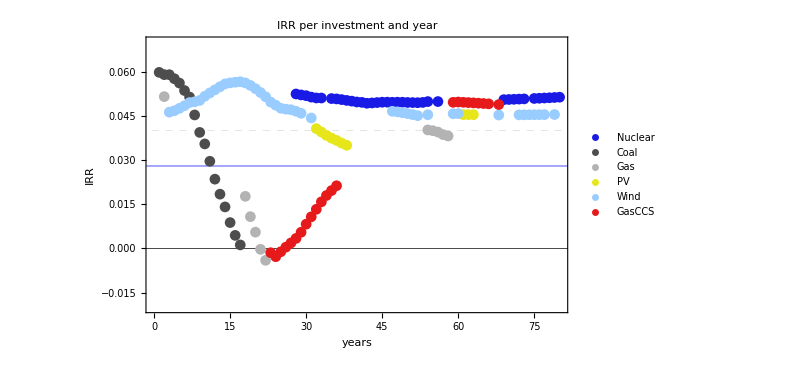

```mathematica
plotTime=endTime;
irrGraph=ListPlot[Table[If[irrCalc[plant,t]≠0,irrCalc[plant,t],-10],{plant,plantTypeList},{t,1,plotTime}],PlotRange->{-0.02,0.07},PlotStyle->colors,PlotLegends->PointLegend[plantTypeList,LabelStyle->16],
PlotLabel->Style["IRR per investment and year",Directive[ 18],FontFamily->"Helvetica"],
ImageSize->600,FrameStyle->Directive[16],
PlotMarkers->{"●",11},
Frame->True,
GridLines->{{},{{0.04(1-fracInvest),Blue},{0.04,Dashed},{0,Black}}},
GridLinesStyle->{Thickness[0.001],Thickness[0.001]},
FrameLabel->{Style["years",FontSize->16,Italic],Style["IRR",FontSize->16,Italic,Black]}]
```

```mathematica
Export["IRR-techn.pdf",irrGraph];
```

```mathematica
Equity
```

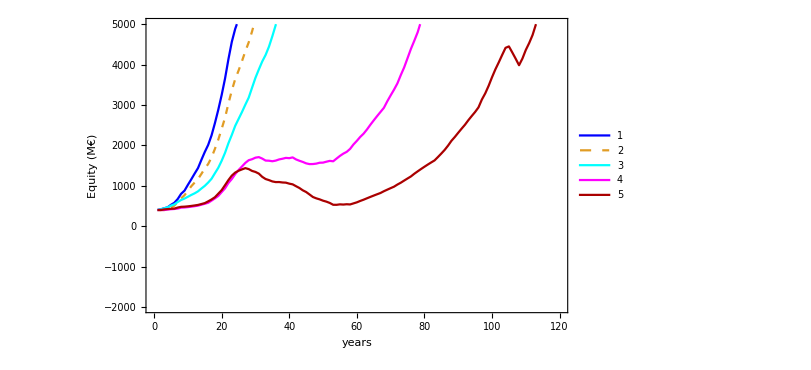

```mathematica
plotTime=endTime+xTime;
compNr1=8;compNr2=9;
compNr1=6;compNr2=10;
compNr1=1;compNr2=20;
compList={1,2,3,4};
compList={1,2,3,4,5}+0;
ListLinePlot[Join[Table[equity[t,comp],{t,1,plotTime},{comp,compList}]ᵀ],PlotStyle->{Blue,Dashed,Cyan,Magenta,Darker[Red],Darker[Green],Brown,Black},Frame->True,PlotRange->{-2000,5000},PlotLegends->Automatic,ImageSize->{600,400},AxesStyle->Directive[12],FrameLabel->{Style["years",FontSize->14,Italic],Style["Equity (M€)",FontSize->14,Italic,Blue]}]
```

Rate of Return based on equity over x year periods

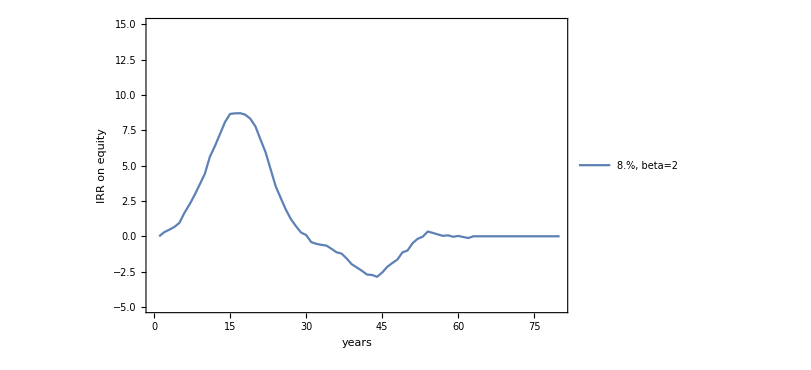

```mathematica
plotTime=endTime;
compList={14};
compList=Range[numComp-1];
compList=Select[compList,#≠10&];
compList={3,7,13};
compList=Range[numComp-1];
compList={1,2,3,4,5};
compList={3,8,13};
compList={1,2,3,4,5};
compList={2};
compList={1,2,3,4,5}+15;
compList=Range[numComp-1];
compList={1,6,11,16};
compList={1,2,3,6,7,8,11,12};
compListAlive={16}+0;
timePeriod=10;
compList=Range[numComp-1];
compList={3,8,13}+0;
compList={1,2,3,6,7,8,12};
compList={1,2,3,4,5};
compList=Range[10];
compListAlive=Select[compList,companyState[[#]]=="alive" &];
compListAlive=compList;
compListAlive={20};
companyIRR=ListLinePlot[Table[100irrCompanyPeriod[company,t1,t1+timePeriod-1],{company,compListAlive},{t1,1,plotTime}],Frame->True,PlotRange->{-5,15},DataRange->{1,plotTime},ImageSize->{600,400},
PlotLegends->Table[
ToString[100companyCharacteristics[[comp,1]]]<>"%,  beta="<>ToString[companyCharacteristics[[comp,2]]]
,{comp,compListAlive}],
FrameLabel->{Style["years",FontSize->14,Italic],Style["IRR on equity",FontSize->14,Italic,Blue]}]
```

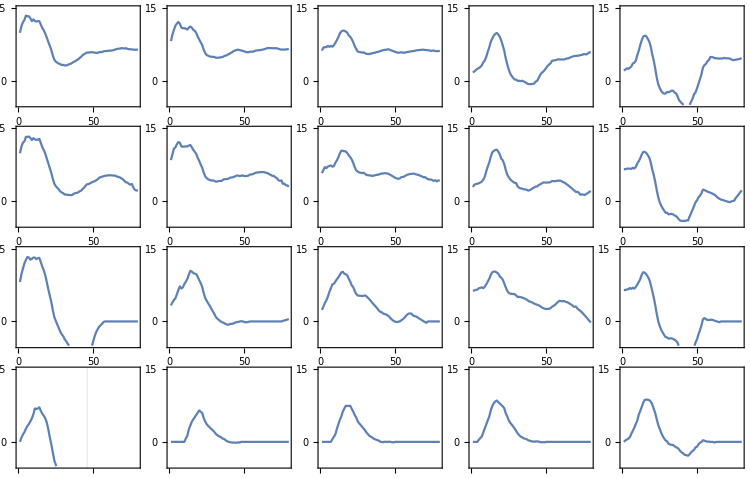

```mathematica
plotTime=90;
plotTime=endTime;
timePeriod=10;
markers=Flatten[Table[Table[{"●",2size+3},{6}],{size,{4,3,2,1}}],1];
maxSize=4;
colorsT=colors[[1;;6]];
Table[irrCalcTable[plant,t]=irrCalc[plant,t],{plant,plantTypeList},{t,1,plotTime}];
irrCompTable=Table[
ListLinePlot[Table[100irrCompanyPeriod[company,t1,t1+timePeriod-1],{t1,1,plotTime}],
Frame->True,PlotRange->{-5,15},DataRange->{1,plotTime},ImageSize->260,AspectRatio->0.8,FrameStyle->Directive[8],
GridLines->{If[companyState[[company]]≠"alive",{companyState[[company]]},{}]},
GridLinesStyle->{Directive[Thickness[0.008],Red],Thickness[0.005]}],
{company,1,numComp}];
irrCompGrid=Partition[irrCompTable,5];
irrCompGridOut=GraphicsGrid[irrCompGrid,Spacings->{Scaled[0.04],Scaled[0.04]},ImageSize->750]
```

```mathematica
Export["IRR-comp-6-10.pdf",companyIRR];
```

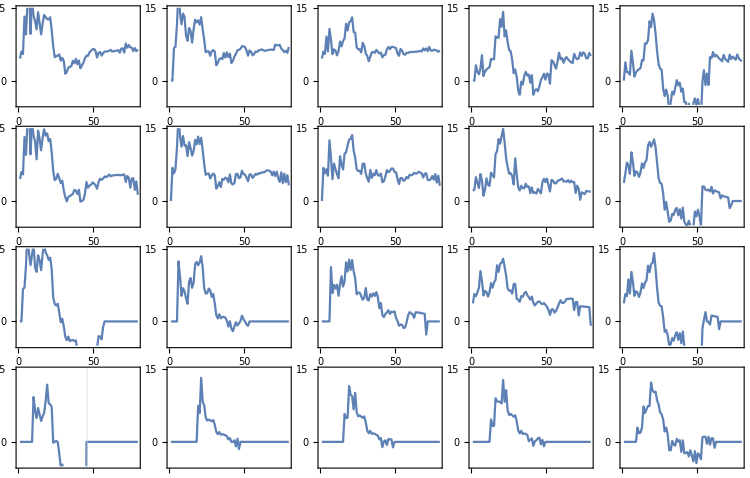

```mathematica
(* Annal ROE *)
plotTime=90;
plotTime=endTime;
timePeriod=10;
markers=Flatten[Table[Table[{"●",2size+3},{6}],{size,{4,3,2,1}}],1];
maxSize=4;
colorsT=colors[[1;;6]];
Table[irrCalcTable[plant,t]=irrCalc[plant,t],{plant,plantTypeList},{t,1,plotTime}];
irrCompTable=Table[
ListLinePlot[
Table[100If[equity[t,company]>0,(equity[t,company]+dividend[t,company])/equity[t-1,company]-1,0,"test2"],{t,2,endTime}],
Frame->True,PlotRange->{-5,15},DataRange->{1,plotTime},ImageSize->260,AspectRatio->0.8,FrameStyle->Directive[8],
GridLines->{If[companyState[[company]]≠"alive",{companyState[[company]]},{}]},
GridLinesStyle->{Directive[Thickness[0.008],Red],Thickness[0.005]}],
{company,1,numComp}];
irrCompGrid=Partition[irrCompTable,5];
irrCompGridOut=GraphicsGrid[irrCompGrid,Spacings->{Scaled[0.04],Scaled[0.04]},ImageSize->750]
```

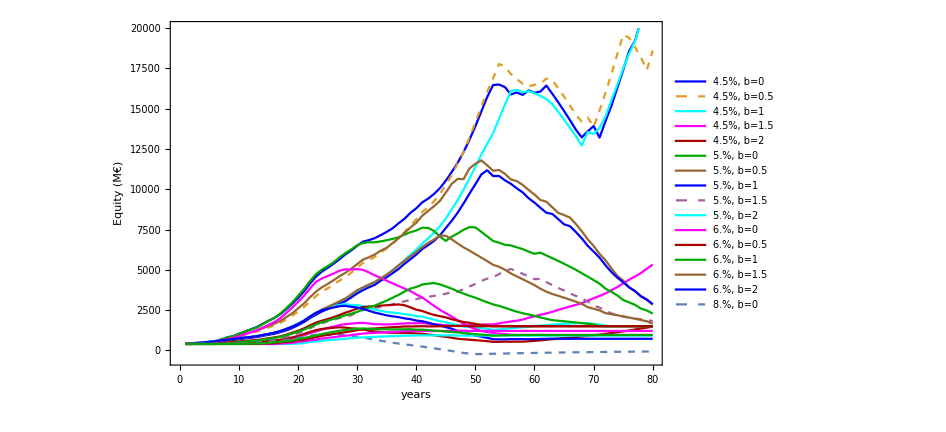

```mathematica
compNr1=8;compNr2=9;
compNr1=1;compNr2=12;
compList={5,8,9};
compList={6,7,8,9,10,11,12};
compList=Range[numComp];
compList={1,2,3,4,5};
compList={6,7,8,9,10};
compList={12,13,14,15,16};
compList={1,2,3};
compList=Range[numComp-1];
compList={1,6,11,16};
compListAlive=Select[compList,companyState[[#]]=="alive" &];
compList=compListAlive;
compList={1,2,3,4,5}+5;
compList=Range[numComp-1];
ListLinePlot[Join[Table[equity[t,comp],{t,1,endTime},{comp,compList}]ᵀ],PlotStyle->{Blue,Dashed,Cyan,Magenta,Darker[Red],Darker[Green],Brown},PlotRange->{-500,20000},Frame->True,FrameStyle->Directive[14],PlotLegends->Table[
ToString[100companyCharacteristics[[comp,1]]]<>"%, b="<>ToString[companyCharacteristics[[comp,2]]]
,{comp,compList}],ImageSize->{700,400},AxesStyle->Directive[12],FrameLabel->{Style["years",FontSize->14,Italic],Style["Equity (M€)",FontSize->14,Italic,Blue]}]
```

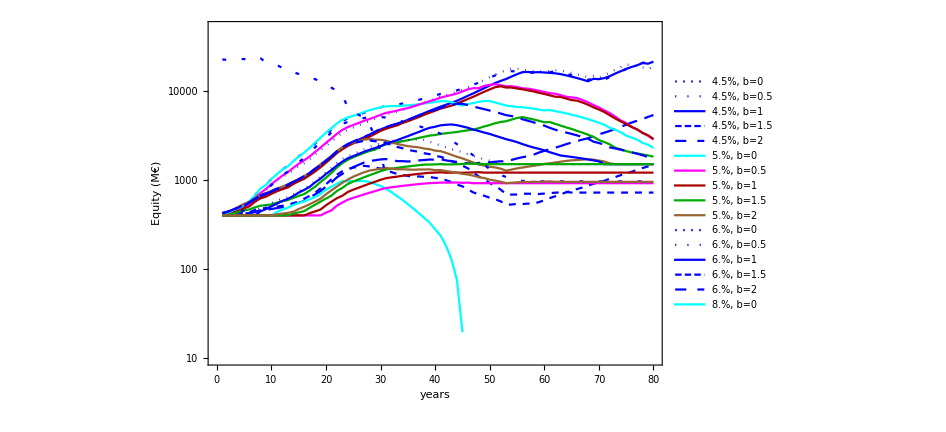

```mathematica
newPlotStyle={{Dashing[{0.004,0.016}],Blue},{Dotted,Blue},Blue,{Dashing[{0.016,0.008}],Blue}};
compNr1=8;compNr2=9;
compNr1=1;compNr2=12;
compList={5,8,9};
compList={6,7,8,9,10,11,12};
compList=Range[numComp];
compList={1,2,3,4,5};
compList={6,7,8,9,10};
compList={12,13,14,15,16};
compList={1,2,3};
compList={1,6,11,16};
compListAlive=Select[compList,companyState[[#]]=="alive" &];
compList=compListAlive;
compList={1,2,3,4,5}+0;
compList=Range[numComp];
ListLogPlot[Join[Table[equity[t,comp],{t,1,endTime},{comp,compList}]ᵀ],PlotStyle->{{Dashing[{0.004,0.016}],Blue},{Dotted,Blue},Blue,{Dashing[{0.016,0.008}],Blue},{Dashed,Blue},Cyan,Magenta,Darker[Red],Darker[Green],Brown},PlotRange->{10,50000},Frame->True,FrameStyle->Directive[14],PlotLegends->Table[
ToString[100companyCharacteristics[[comp,1]]]<>"%, b="<>ToString[companyCharacteristics[[comp,2]]]
,{comp,compList}],ImageSize->{700,400},AxesStyle->Directive[12],FrameLabel->{Style["years",FontSize->14,Italic],Style["Equity (M€)",FontSize->14,Italic,Blue]},Joined->True]
```

```mathematica
Bank account money
```

account Bank money

```mathematica
Select[Table[{i,companyState[[i]]},{i,1,numComp}],#[[2]]=="bankrupt"&]
```

{}

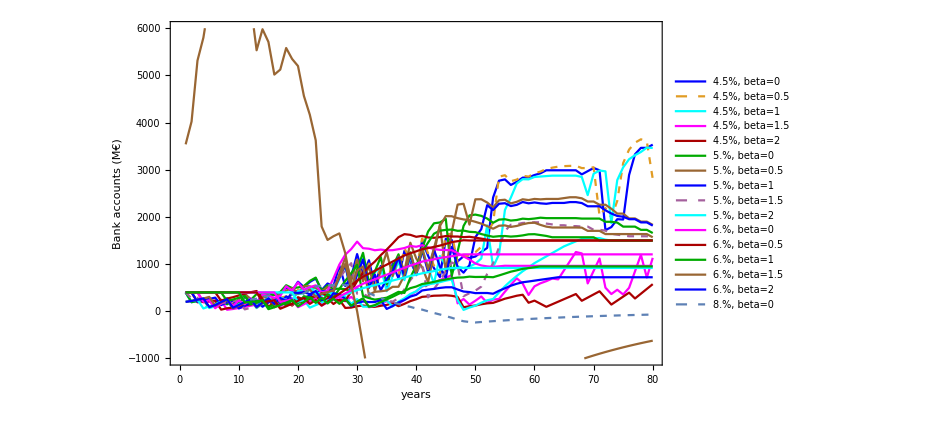

```mathematica
compList={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16};
compList={12,13,14,15,16};
compList=Range[numComp];
compList={16}+0;
compList={5}+0;
compList={1,2,3,4,5}+15;
compList=Range[numComp];
ListLinePlot[Table[Table[bankAccount[t,company],{t,1,endTime}],{company,compList}],Frame->True,PlotRange->{-1000,6000},PlotStyle->{Blue,Dashed,Cyan,Magenta,Darker[Red],Darker[Green],Brown},PlotLegends->Table[
ToString[100companyCharacteristics[[comp,1]]]<>"%,  beta="<>ToString[companyCharacteristics[[comp,2]]]
,{comp,compList}],ImageSize->{700,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["Bank accounts (M€)",FontSize->14,Italic,Blue]}]
```

```mathematica
Electricity price (¢/kWh)
```

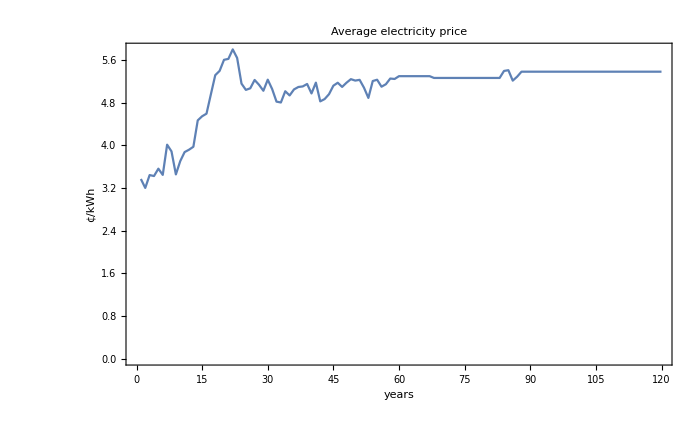

```mathematica
ListLinePlot[Table[averageElecPrice[t],{t,1,tout+1}],PlotRange->Full,ImageSize->{700,500},Frame->True,AxesOrigin->{0,0},PlotLabel->Style["Average electricity price",Directive[18],FontFamily->"Helvetica"],
FrameLabel->{Style["years",FontSize->16,Italic],Style["¢/kWh",FontSize->16,Italic]},FrameStyle->Directive[16]]
```

```mathematica
Installed capacity
```

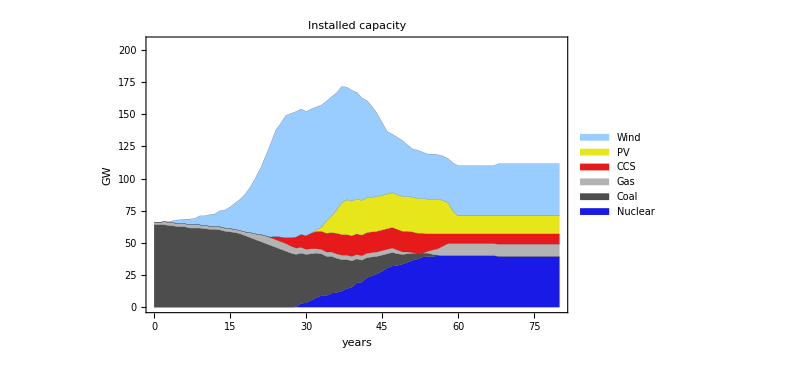

```mathematica
capitalFigure=graphDynCapitalL[endTime]
```

```mathematica
Export["capacity.pdf",capitalFigure];
```

```mathematica
Electricity price (¢/kWh)
```

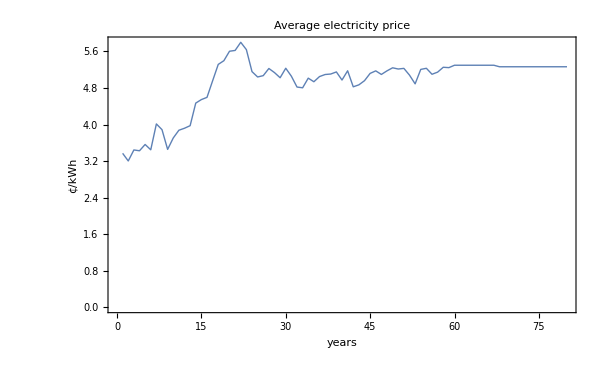

```mathematica
plotTime=endTime;
ePrice=ListLinePlot[Table[averageElecPrice[t],{t,1,plotTime}],PlotRange->Full,ImageSize->{600,400},AxesOrigin->{0,0},FrameLabel->{Style["years",FontSize->14,Italic],Style["¢/kWh",FontSize->16,Italic]},FrameStyle->Directive[16],Frame->True,PlotStyle->Thick,PlotLabel->Style["Average electricity price",Directive[18],FontFamily->"Helvetica"]]
```

```mathematica
Export["ePrice.pdf",ePrice];
```

Electricity production

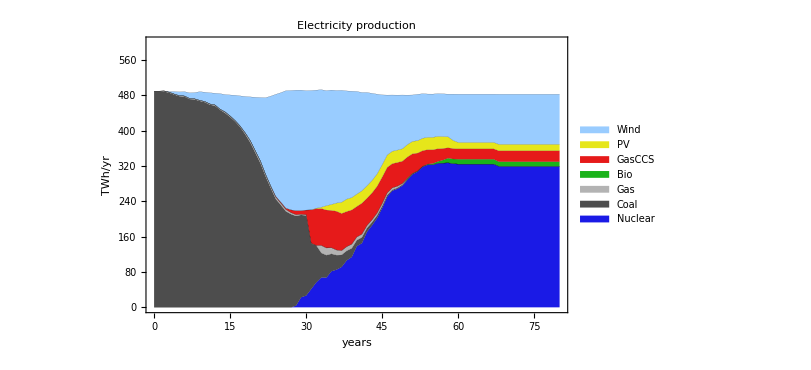

```mathematica
elecProd=graphElectricityX[endTime]
```

```mathematica
Annual CO2 emissions (Mton)
```

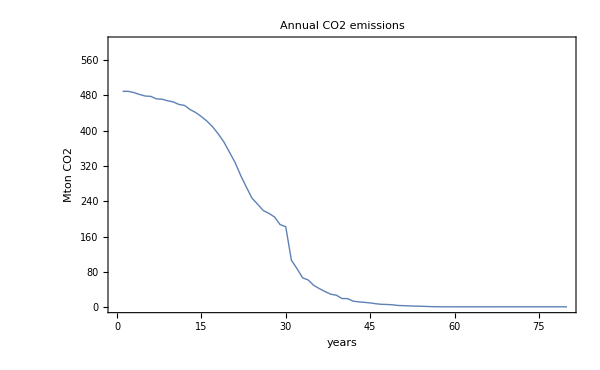

```mathematica
plotTime=80;
ePrice=ListLinePlot[Table[emissions[t],{t,0,plotTime}],PlotRange->{0,600},Frame->True,DataRange->{0,plotTime},
PlotLabel->Style["Annual CO2 emissions",Directive[18],FontFamily->"Helvetica"],PlotStyle->Thick,FrameLabel->{Style["years",FontSize->16,Italic],Style["Mton CO2",FontSize->16,Italic,Black]},ImageSize->{600,400},FrameStyle->Directive[16]]
```

```mathematica
Export["ePrice.pdf",ePrice];
```

```mathematica
Investments (M€)
```

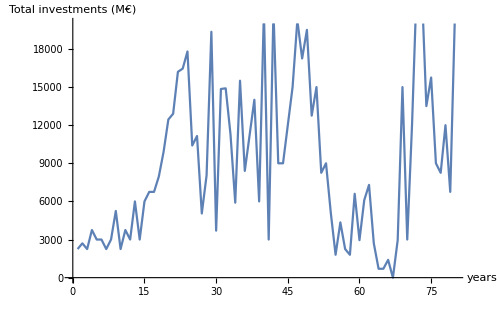

```mathematica
ListLinePlot[Table[Sum[invest[pl,year]unitSize capCost[pl]/1000.,{pl,plantTypeList}],{year,1,endTime}],PlotRange->{0,20000},AxesLabel->{Style["years",FontSize->14,Italic],Style["Total investments (M€)",FontSize->14,Italic,Blue]},ImageSize->{500,300},AxesStyle->Directive[14]]
```

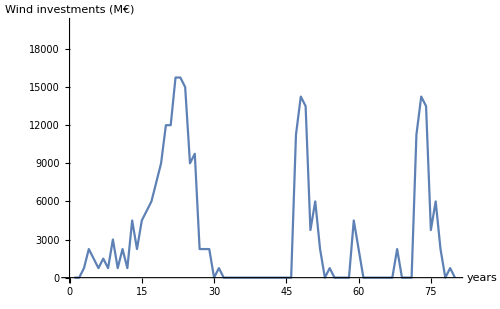

```mathematica
ListLinePlot[Table[Sum[invest[pl,year]unitSize capCost[pl]/1000.,{pl,{Wind}}],{year,1,endTime}],PlotRange->{0,20000},AxesLabel->{Style["years",FontSize->14,Italic],Style["Wind investments (M€)",FontSize->14,Italic,Blue]},ImageSize->{500,300},AxesStyle->Directive[14]]
```

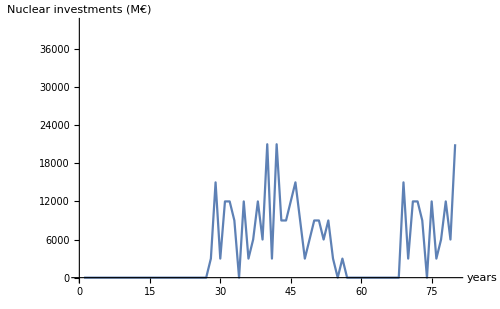

```mathematica
ListLinePlot[Table[Sum[invest[pl,year]unitSize capCost[pl]/1000.,{pl,{Nuclear}}],{year,1,endTime}],PlotRange->{0,40000},AxesLabel->{Style["years",FontSize->14,Italic],Style["Nuclear investments (M€)",FontSize->14,Italic,Blue]},ImageSize->{500,300},AxesStyle->Directive[14]]
```

```mathematica
Annual net profit (net revenues – annuitized capital cost); in M€
```

in M€

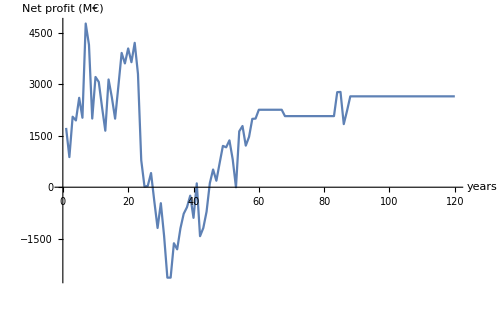

```mathematica
ListLinePlot[Table[Sum[netProfit[pl,t,comp],{comp,1,numComp},{pl,plantTypeList}],{t,1,endTime+xTime}],AxesLabel->{Style["years",FontSize->14,Italic],Style["Net profit (M€)",FontSize->14,Italic,Blue]},ImageSize->{500,300},AxesStyle->Directive[14]]
```

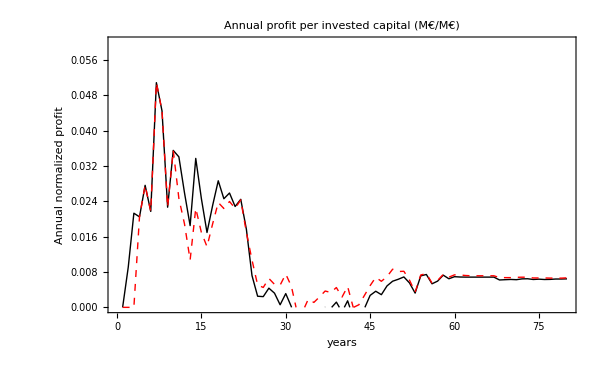

```mathematica
tPlot=80;
compList={6,7,8,9,10};
compList={1,2,3,4,5};
compList={1,2,3,4,5,6,7,8,9,10};
compList={5,10,15,20};
compList={7,8,9};
compList={17,18,19};
compList={2,3,4};
compList={2,3,4,9,14,19};
compList={1};
compList={1,2,3,4,5,6};
compList=Range[numComp];
compList={1,11,14,15,16};
compList={1};
compList=Range[numComp-1];
compList={1,2};
plotTime=endTime+xTime;
Table[totInvCost[t,comp]=Sum[capitalComp[plant,t,comp]capCost[plant]/1000,{plant,plantTypeList}],{t,1,tPlot},{comp,compList}];
netProfHomog=ListLinePlot[Table[Sum[netProfit[pl,t,comp]/(totInvCost[t,comp]+0.001),{pl,plantTypeList}],{comp,compList},{t,1,tPlot}],
Frame->True,
PlotStyle->{{Black,Thick},{Dashed,Red,Thick},{Dashed,Black,Thick},{Blue,Thick}},
FrameLabel->{Style["years",FontSize->14,Italic],Style["Annual normalized profit",FontSize->14,Italic]},ImageSize->{600,400},FrameStyle->Directive[14],ImagePadding->{{60,10},{50,5}},
PlotRange->{0,0.06},
(*PlotLegends->Placed[Table[ToString[companyCharacteristics[[comp,2]]],{comp,compList}],{0.88,0.2}],*)PlotLabel->Style["Annual profit per invested capital (M€/M€)",Directive[16],FontFamily->"Helvetica"]]
```

```mathematica
Export["netProf-homog-new.pdf",netProfHomog];
```

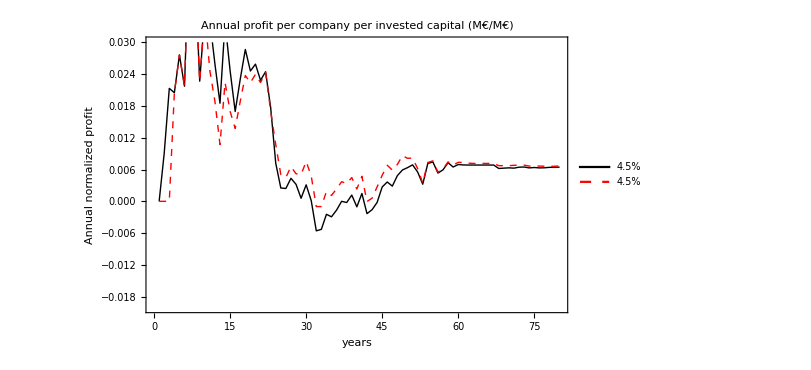

```mathematica
tPlot=endTime;
compList={6,7,8,9,10};
compList={1,2,3,4,5};
compList={1,2,3,4,5,6,7,8,9,10};
compList={5,10,15,20};
compList={7,8,9};
compList={17,18,19};
compList={2,3,4};
compList={2,3,4,9,14,19};
compList={1};
compList={1,2,3,4,5,6};
compList=Range[numComp];
compList={1,11,14,15,16};
compList={1,2,3,4};
compList={1,2}+0;
plotTime=endTime+xTime;
Table[totInvCost[t,comp]=Sum[capitalComp[plant,t,comp]capCost[plant]/1000,{plant,plantTypeList}],{t,1,tPlot},{comp,compList}];
netProfHHR=ListLinePlot[Table[Sum[netProfit[pl,t,comp]/(totInvCost[t,comp]+0.001),{pl,plantTypeList}],{comp,compList},{t,1,tPlot}],
Frame->True,PlotRange->{-0.02,0.03},
PlotStyle->{{Black,Thick},{Dashed,Red,Thick},{Dashed,Black,Thick},{Blue,Thick}},
FrameLabel->{Style["years",FontSize->14,Italic],Style["Annual normalized profit",FontSize->14,Italic]},ImageSize->{600,400},FrameStyle->Directive[14],ImagePadding->{{60,10},{50,5}},
PlotLegends->Placed[Table[ToString[100companyCharacteristics[[comp,1]]]<>"%",{comp,compList}],{0.88,0.2}],PlotLabel->Style["Annual profit per company per invested capital (M€/M€)",Directive[16],FontFamily->"Helvetica"]]
```

```mathematica
Export["netProf-HHR-new.pdf",netProfHHR];
```

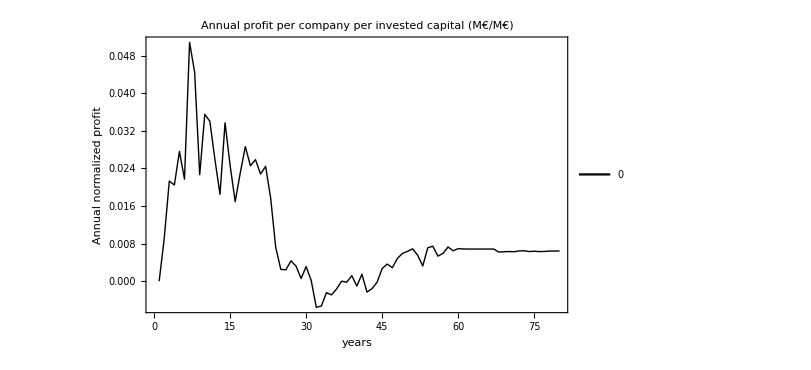

```mathematica
tPlot=80;
compList={6,7,8,9,10};
compList={1,2,3,4,5};
compList={1,2,3,4,5,6,7,8,9,10};
compList={5,10,15,20};
compList={7,8,9};
compList={17,18,19};
compList={2,3,4};
compList={2,3,4,9,14,19};
compList={1};
compList={1,2,3,4,5,6};
compList=Range[numComp];
compList={1,11,14,15,16};
compList={1};
plotTime=endTime+xTime;
Table[totInvCost[t,comp]=Sum[capitalComp[plant,t,comp]capCost[plant]/1000,{plant,plantTypeList}],{t,1,tPlot},{comp,compList}];
netProfHF=ListLinePlot[Table[Sum[netProfit[pl,t,comp]/(totInvCost[t,comp]+0.001),{pl,plantTypeList}],{comp,compList},{t,1,tPlot}],
Frame->True,
PlotStyle->{{Black,Thick},{Dashed,Red,Thick},{Dashed,Black,Thick},{Blue,Thick}},
FrameLabel->{Style["years",FontSize->14,Italic],Style["Annual normalized profit",FontSize->14,Italic]},ImageSize->{600,400},FrameStyle->Directive[14],ImagePadding->{{60,10},{50,5}},
PlotLegends->Placed[Table[ToString[companyCharacteristics[[comp,2]]],{comp,compList}],{0.88,0.2}],PlotLabel->Style["Annual profit per company per invested capital (M€/M€)",Directive[16],FontFamily->"Helvetica"]]
```

```mathematica
Export["netProf-HF-new.pdf",netProfHF];
```

Eletricity price variation

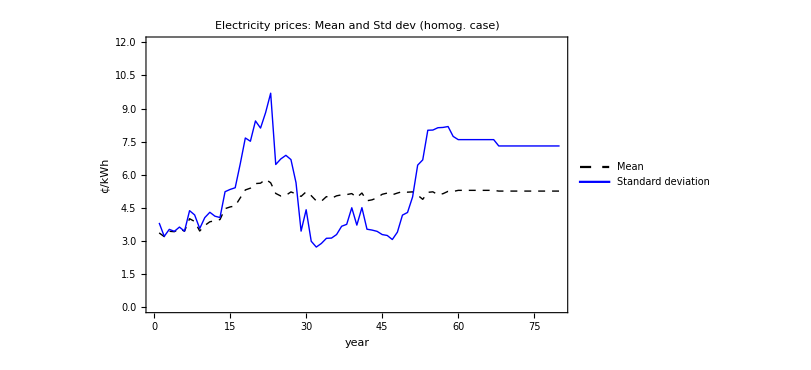

```mathematica
stdDev=ListLinePlot[Table[{averageElecPrice[t],priceStandardDev[t]},{t,1,80}]ᵀ,PlotRange->{0,12},PlotStyle->{{Dashed,Black,Thick},{Blue,Thick}},PlotLegends->Placed[{ "Mean","Standard deviation"},{0.84,0.1}],Frame->True,ImageSize->{600,400},FrameLabel->{"year","¢/kWh"},FrameStyle->Directive[Thickness[0.0012],16],PlotLabel->Style["Electricity prices: Mean and Std dev (homog. case)",Directive[18],FontFamily->"Helvetica"]]
```

```mathematica
Export["stdDev-homog.pdf",stdDev];
```

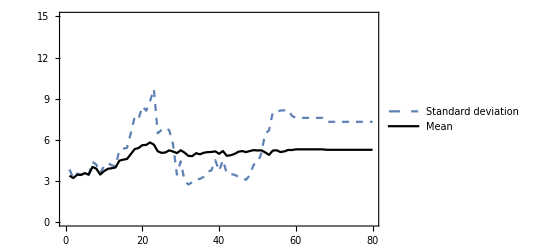

```mathematica
ListLinePlot[Table[{priceStandardDev[t],averageElecPrice[t]},{t,1,80}]ᵀ,PlotRange->{0,15},PlotStyle->{{Dashed,Thick},{Black,Thick}},PlotLegends->{"Standard deviation", "Mean"},Frame->True]
```

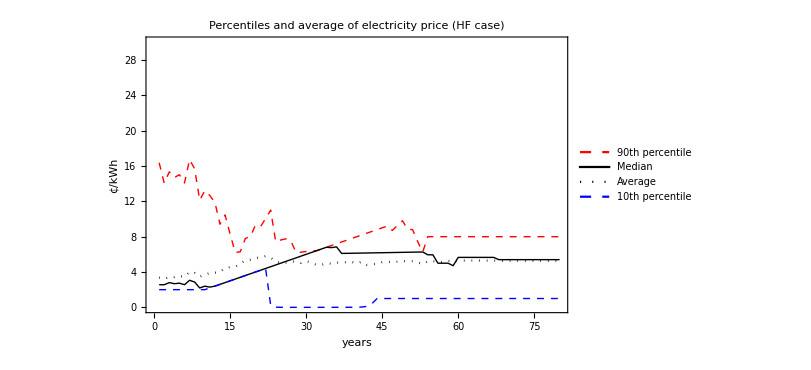

```mathematica
q=0.05;
percentiles=ListLinePlot[Table[{priceQuantiles[t,1-q],priceQuantiles[t,0.5],averageElecPrice[t],priceQuantiles[t,q]},{t,1,80}]ᵀ,PlotStyle->{{Dashed,Red,Thick},{Black,Thick},{Dotted,Black},{Dashed,Blue,Thick}},PlotRange->{0,30},PlotLegends->Placed[LineLegend[{"90th percentile", "Median","Average", "10th percentile"},LabelStyle->14],{0.88,0.84}],Frame->True,
ImageSize->{600,400},FrameStyle->Directive[Thickness[0.0012],16],FrameLabel->{Style["years",FontSize->16,Italic],Style["¢/kWh",FontSize->16,Italic,Black]},
PlotLabel->Style["Percentiles and average of electricity price (HF case)",Directive[18],FontFamily->"Helvetica"]]
```

```mathematica
Export["percentiles-10-90_HF2.pdf",percentiles];
```

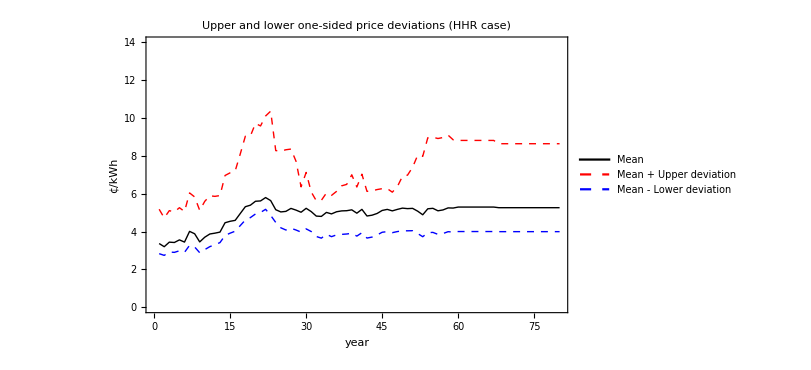

```mathematica
onesidedDevs=ListLinePlot[Table[{averageElecPrice[t],averageElecPrice[t]+priceUpperStd[t],averageElecPrice[t]-priceLowerStd[t]},{t,1,80}]ᵀ,PlotRange->{0,14},PlotStyle->{{Thick,Black},{Dashed,Red,Thick},{Dashed,Blue,Thick}},PlotLegends->Placed[{ "Mean","Mean + Upper deviation","Mean - Lower deviation"},{0.84,0.1}],Frame->True,ImageSize->{600,400},FrameLabel->{"year","¢/kWh"},FrameStyle->Directive[Thickness[0.0012],16],PlotLabel->Style["Upper and lower one-sided price deviations (HHR case)",Directive[18],FontFamily->"Helvetica"]]
```

```mathematica
Export["onesidedDevs-HHR.pdf",onesidedDevs];
```

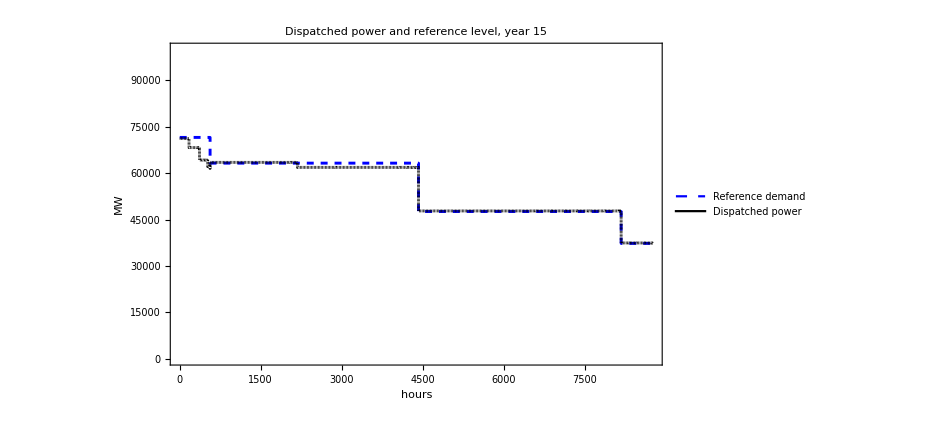

```mathematica
timeT=15;
{a,b}=quantityHoursFigure[timeT];
dispatchedPower=ListPlot[{a,b},Joined->True,PlotStyle->{{Dashed,Blue,Thickness[0.003]},{Black,Dashing[0],Thickness[0.003]}},Frame->True,PlotRange->{0,100000},ImageSize->{700,500},FrameStyle->Directive[Thickness[0.002],16],FrameLabel->{Style["hours",FontSize->16,Italic],Style["MW",FontSize->16,Italic,Black]},
PlotLegends->Placed[LineLegend[{{Blue,Dashed},Black},{"Reference demand", "Dispatched power"},LabelStyle->16],{0.8,0.1}],
PlotLabel->Style["Dispatched power and reference level, year "<>ToString[timeT],Directive[18],FontFamily->"Helvetica"]]
```

```mathematica
Export["dispatchedPower-t5.pdf",dispatchedPower];
```

Electricity price-production histograms

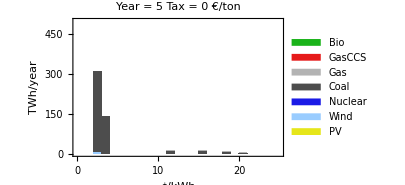
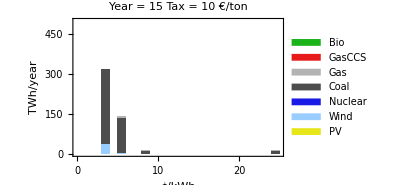
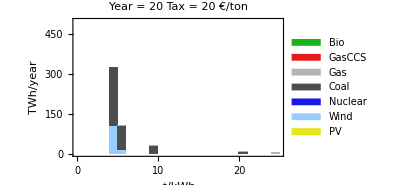
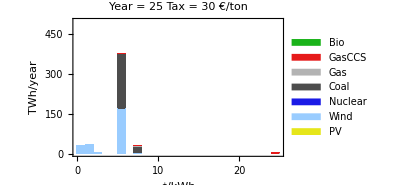
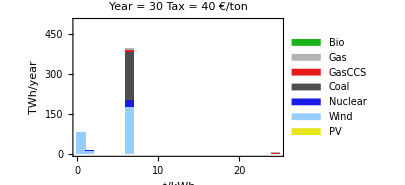
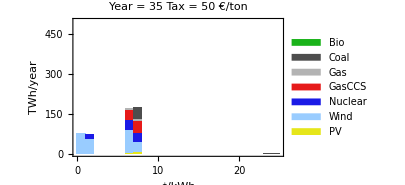
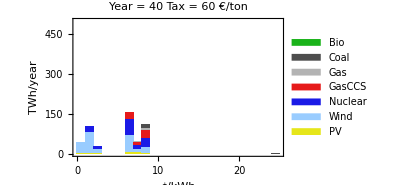
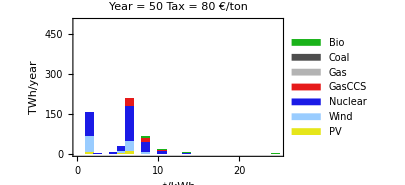

```mathematica
pHist=Table[priceHistogram[tt,500,25,{300,200}],{tt,{5,15,20,25,30,35,40,50,70,80}}]
```

```mathematica
Table[Export["histogram"<>ToString[i]<>".pdf",pHist[[i]]],{i,1,10}];
```

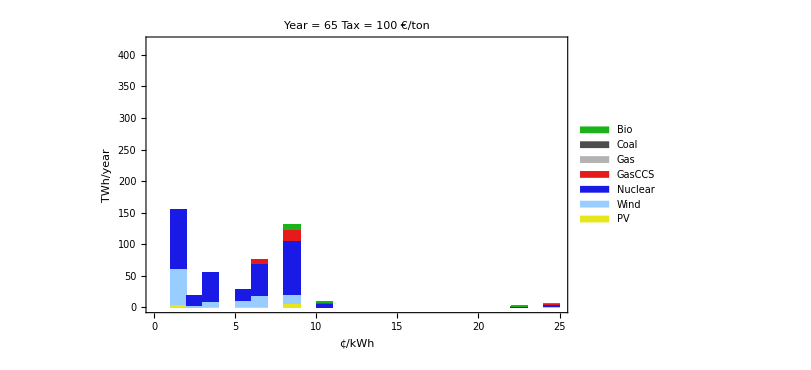

```mathematica
hTime=65;
price80=priceHistogram[hTime,420,25,{600,400}]
```

```mathematica
graphElectricityX[endTime]
```

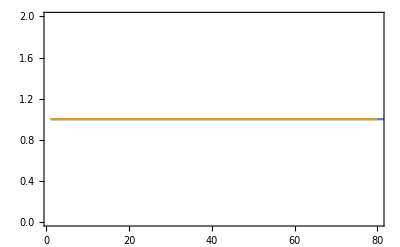

```mathematica
ListLinePlot[{demFactor,Table[1,{endTime}]},PlotRange->{{1,endTime},{Min[demFactor[[1;;endTime]]],Max[demFactor[[1;;endTime]]]}},AxesOrigin->{1,0},Frame->True]
```

Profitability

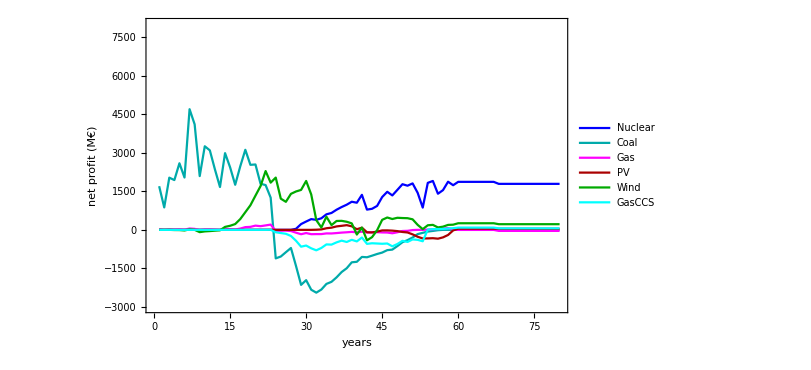

```mathematica
ListLinePlot[Table[Sum[netProfit[plantTypeList[[p]],t,i],{i,1,numComp}],{t,1,endTime},{p,1,nPlantTypes}]ᵀ,PlotRange->{{0,endTime},{-3000,8000}},PlotStyle->{Blue,Darker[Cyan],Magenta,Darker[Red],Darker[Green],Cyan},PlotLegends->plantTypeList,ImageSize->{600,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["net profit (M€)",FontSize->14,Italic,Blue]},Frame->True]
```

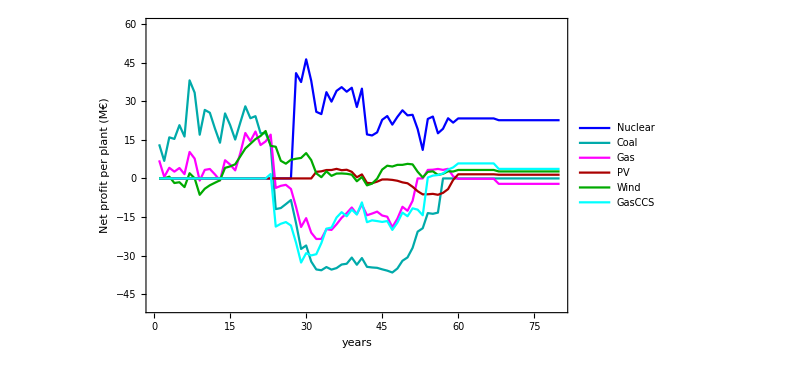

```mathematica
ListLinePlot[Table[Sum[netProfit[plantTypeList[[p]],t,i],{i,1,numComp}]/(capital[plantTypeList[[p]],t]/unitSize+0.0001),{t,1,endTime},{p,1,nPlantTypes}]ᵀ,PlotRange->{{0,endTime},{-50,60}},PlotStyle->{Blue,Darker[Cyan],Magenta,Darker[Red],Darker[Green],Cyan},PlotLegends->plantTypeList,ImageSize->{600,400},AxesStyle->Directive[12],FrameLabel->{Style["years",FontSize->14,Italic],Style["Net profit per plant (M€)",FontSize->14,Italic,Blue]},Frame->True]
```

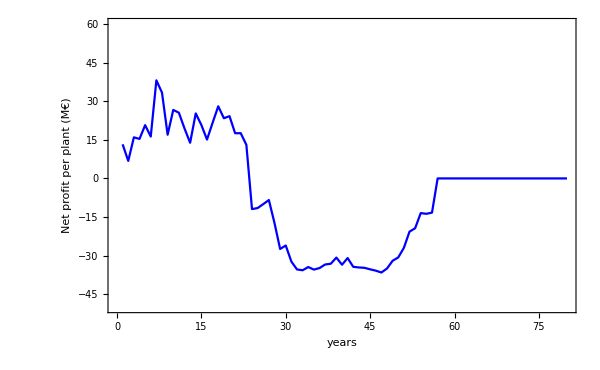

```mathematica
plantNum=2;
ListLinePlot[Table[Sum[netProfit[plantTypeList[[p]],t,i],{i,1,numComp}]/(capital[plantTypeList[[p]],t]/unitSize+0.0001),{t,1,endTime},{p,{plantNum}}]ᵀ,PlotRange->{{0,endTime},{-50,60}},PlotStyle->{Blue,Darker[Cyan],Magenta,Darker[Red],Darker[Green],Cyan},PlotLegends->plantTypeList[[plantNum]],ImageSize->{600,400},AxesStyle->Directive[12],FrameLabel->{Style["years",FontSize->14,Italic],Style["Net profit per plant (M€)",FontSize->14,Italic,Blue]},Frame->True]
```

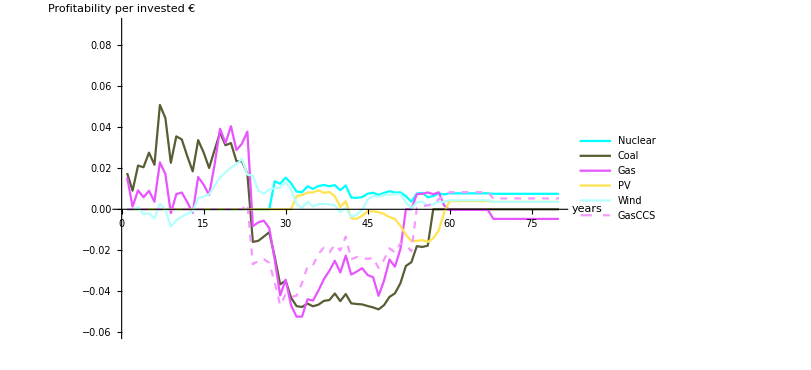

```mathematica
ListLinePlot[Table[Sum[netProfit[pl,t,i],{i,1,numComp}]/(capital[pl,t]capCost[pl]/1000+0.0001),{t,1,endTime},{pl,plantTypeList}]ᵀ,PlotRange->{{0,endTime},{-0.06,0.09}},PlotStyle->colors2style,PlotLegends->plantTypeList,ImageSize->{600,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["Profitability per invested €",FontSize->14,Italic,Blue]}]
```

IRR per plant investment

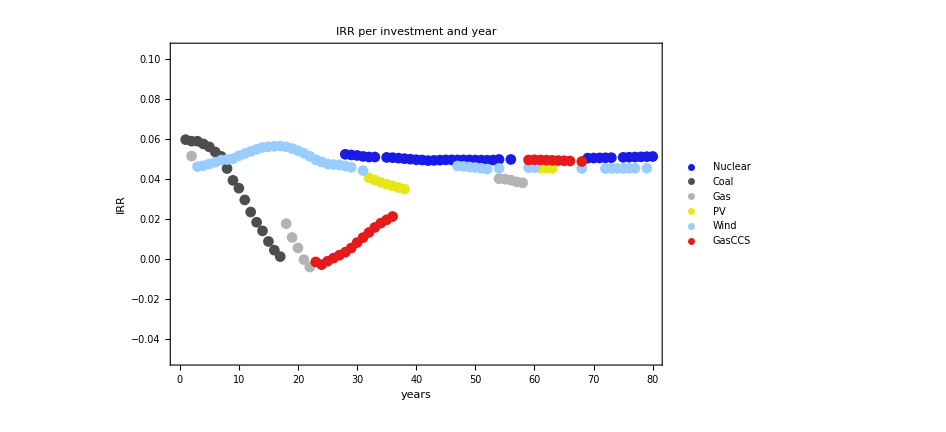

```mathematica
irrGraph=ListPlot[Table[If[irrCalc[plant,t]≠0,irrCalc[plant,t],-10],{plant,plantTypeList},{t,1,80}],PlotRange->{-0.05,0.105},PlotStyle->colors,PlotLegends->PointLegend[plantTypeList,LabelStyle->16],PlotLabel->Style["IRR per investment and year",Directive[ 18],FontFamily->"Helvetica"],
ImageSize->{700,400},FrameStyle->Directive[16],
PlotMarkers->{"●",11},
Frame->True,FrameLabel->{Style["years",FontSize->16,Italic],Style["IRR",FontSize->16,Italic,Black]}]
```

Rate of Return based on equity over x year periods

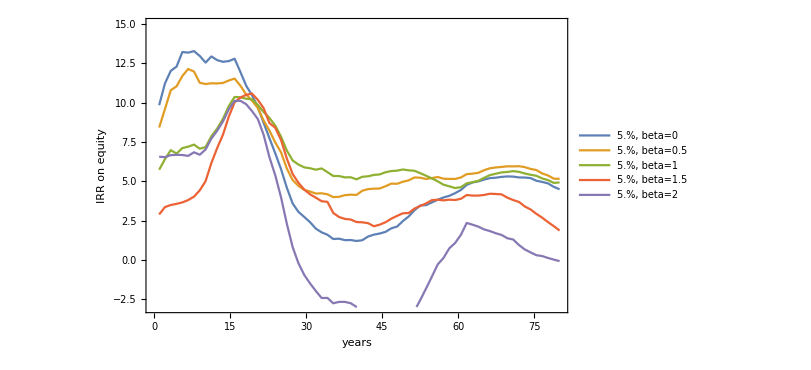

```mathematica
compList={14};
compList=Range[numComp-1];
compList=Select[compList,#≠10&];
compList={3,7,13};
compList=Range[numComp-1];
compList={1,2,3,4,5};
compList={3,8,13};
compList={1,2,3,4,5};
compList={6,7,8,9};
compList={1,6,11,16}+2;
compList={1,2,3,4,5}+5;
timePeriod=10;
ListLinePlot[Table[100irrCompanyPeriod[company,t1,t1+timePeriod-1],{company,compList},{t1,1,70}],Frame->True,PlotRange->{-3,15},DataRange->{1,80},ImageSize->{600,400},
PlotLegends->Table[
ToString[100companyCharacteristics[[comp,1]]]<>"%,  beta="<>ToString[companyCharacteristics[[comp,2]]]
,{comp,compList}],
FrameLabel->{Style["years",FontSize->14,Italic],Style["IRR on equity",FontSize->14,Italic,Blue]}]
```

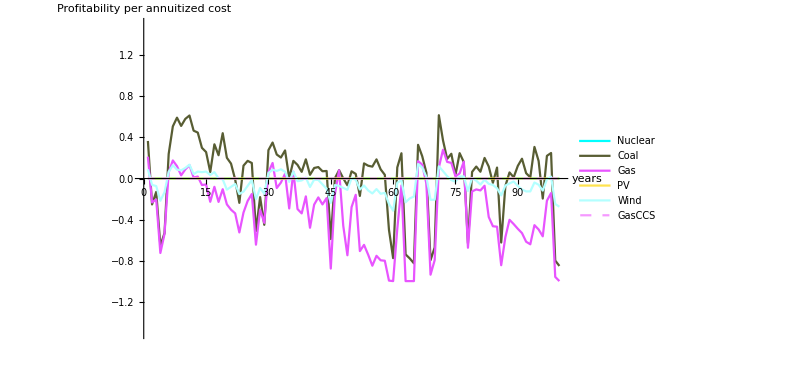

```mathematica
ListLinePlot[Table[Sum[netProfit[pl,t,i],{i,1,numComp}]/(capital[pl,t]capCost[pl]/1000 interest/(1-(1+interest)^(-lifeTime[pl]))+0.0001),{t,1,endTime},{pl,plantTypeList}]ᵀ,PlotRange->{{0,endTime},{-1.5,1.5}},PlotStyle->colors2style,PlotLegends->plantTypeList,ImageSize->{600,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["Profitability per annuitized cost",FontSize->14,Italic,Blue]}]
```

```mathematica
Bank account money
```

```mathematica
Select[Table[{i,companyState[[i]]},{i,1,numComp}],#[[2]]=="bankrupt"&]
```

{}

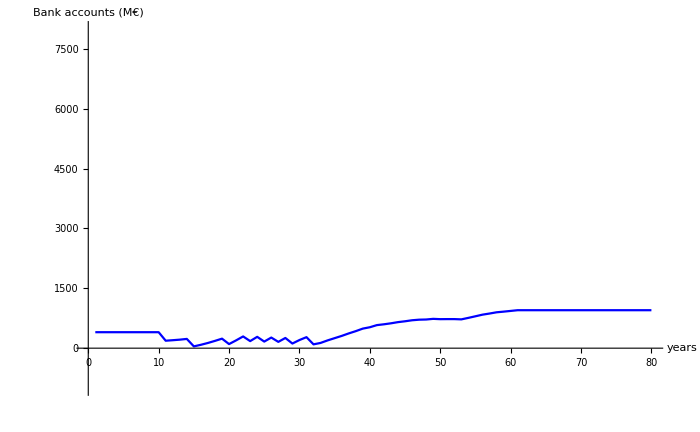

```mathematica
compList={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16};
compList={12,13,14,15,16};
compList=Range[numComp];
compList={1,2,3,4,5};
compList={20};
ListLinePlot[Table[Table[bankAccount[t,company],{t,1,endTime}],{company,compList}],PlotRange->{-1000,8000},PlotStyle->{Blue,Dashed,Cyan,Magenta,Darker[Red],Darker[Green],Brown},PlotLegends->Automatic,ImageSize->{700,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["Bank accounts (M€)",FontSize->14,Italic,Blue]}]
```

```mathematica
Equity
```

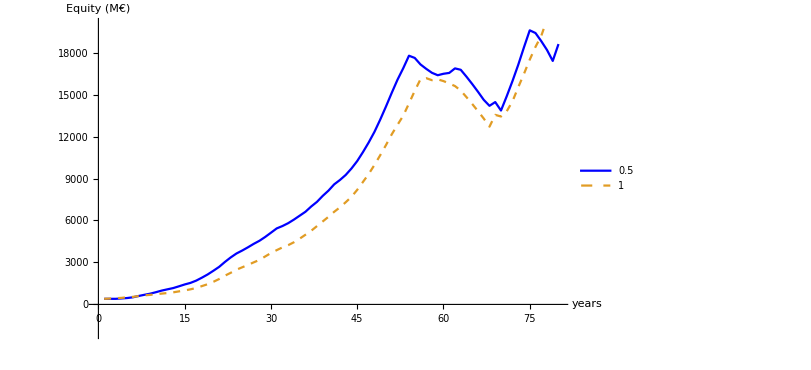

```mathematica
compNr1=8;compNr2=9;
compNr1=1;compNr2=12;
compList={5,8,9};
compList={6,7,8,9,10,11,12};
compList=Range[numComp];
compList={1,2,3,4,5};
compList={6,7,8,9,10};
compList={12,13,14,15,16};
compList=Range[numComp];
compList={2,3};
ListLinePlot[Join[Table[equity[t,comp],{t,1,endTime},{comp,compList}]ᵀ],PlotStyle->{Blue,Dashed,Cyan,Magenta,Darker[Red],Darker[Green],Brown},PlotRange->{-2000,20000},PlotLegends->Table[companyCharacteristics[[comp,2]],{comp,compList}],ImageSize->{600,400},AxesStyle->Directive[12],AxesLabel->{Style["years",FontSize->14,Italic],Style["Equity (M€)",FontSize->14,Italic,Blue]}]
```

Capacity per company

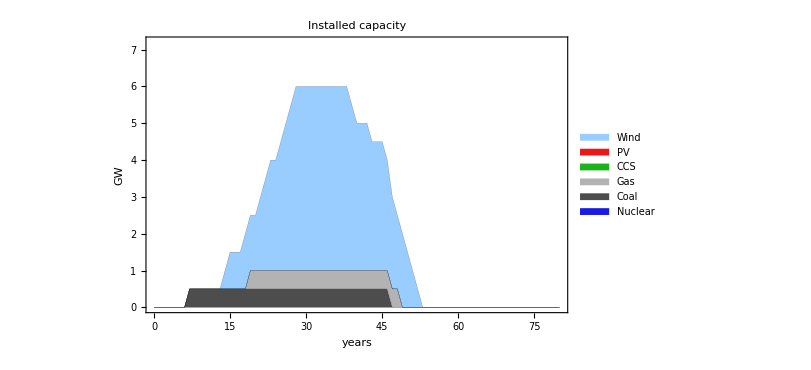

```mathematica
compCapac=graphDynCapitalCompLS[80,12]
```

```mathematica
Export["comp1capacity.pdf",compCapac];
```

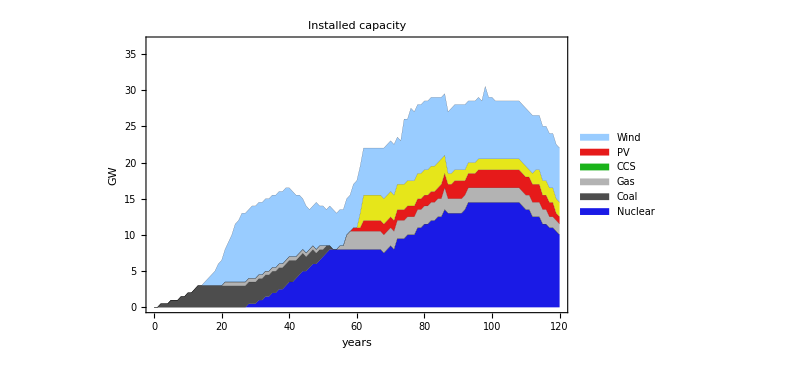
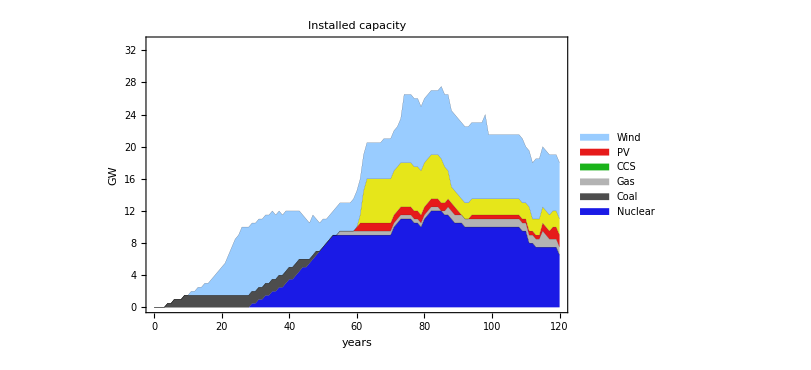
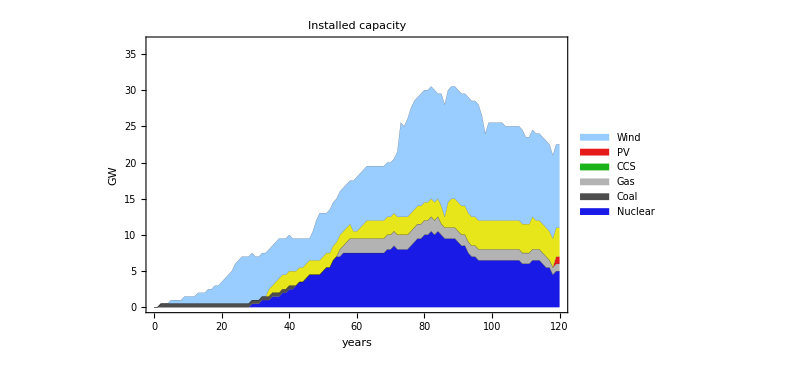
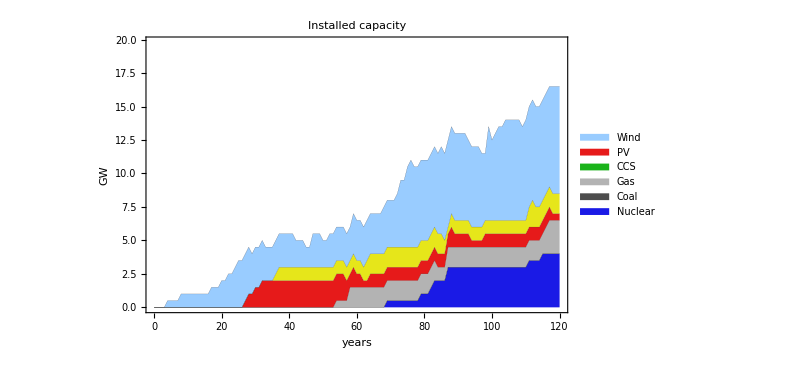
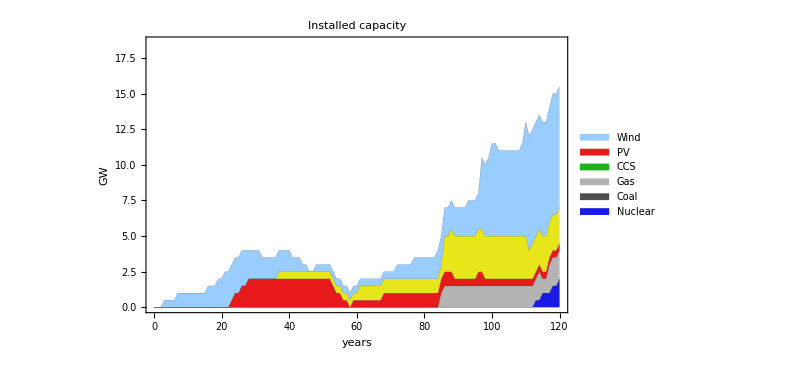
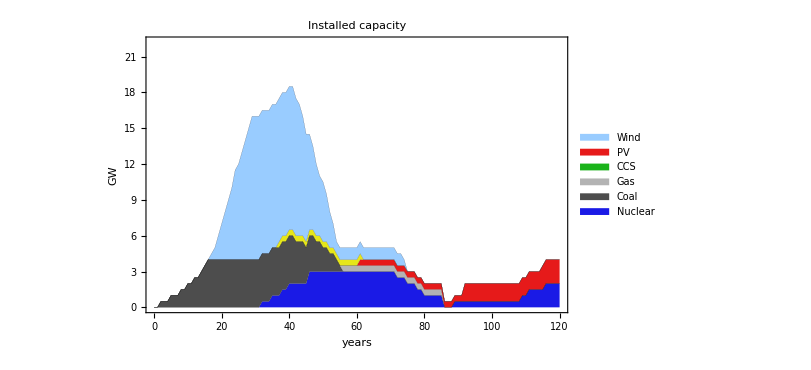
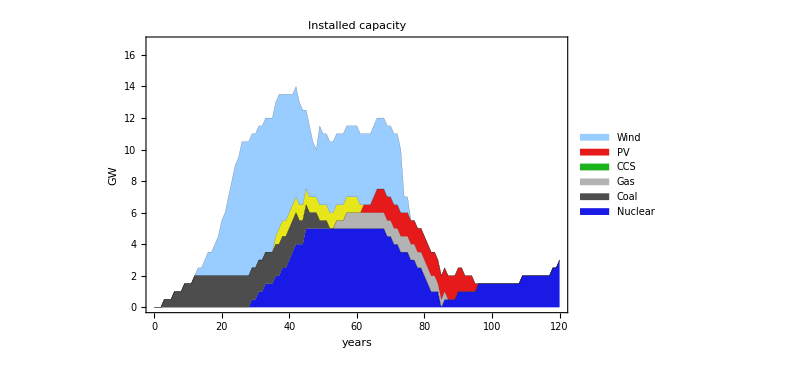
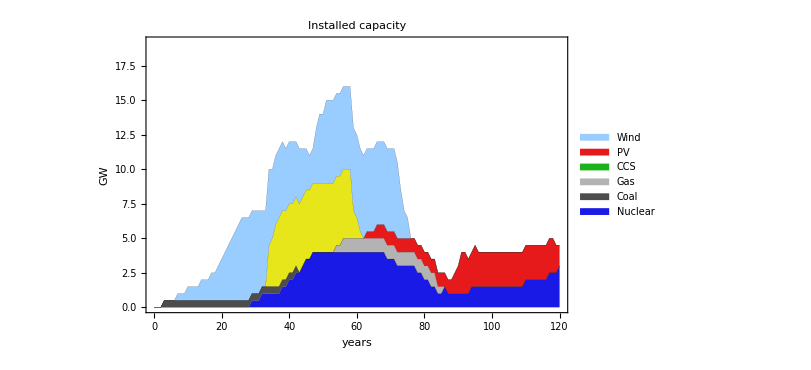

```mathematica
Table[graphDynCapitalCompLS[tout+1,i],{i,1,numComp}]
```